```mathematica
A=(x^2+y^2-2 x)^2==24 (x^2+y^2);
B = Sin[2 x+y]==4 y-3 x+2;
sol=NSolve[{A, B},{x,y},Reals]
```

{{x→-2.42842,y→-2.54634},{x→5.35279,y→3.75188}}

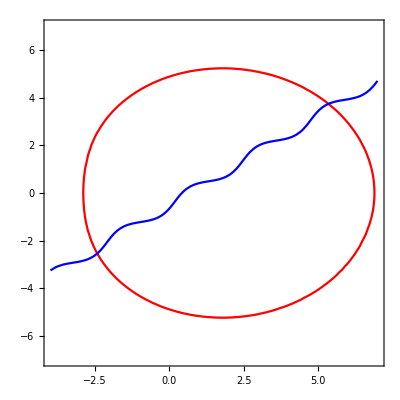

```mathematica
plot1=ContourPlot[Evaluate[A],{x,-4,7},{y,-7,7},ContourStyle->Red];
plot2=ContourPlot[Evaluate[B],{x,-4,7},{y,-7,7},ContourStyle->Blue];
Show[plot1,plot2]
```